## Discrete-time Constant-size Model with Seed Dormancy

### Differential Equations

Matching-alleles model with Seed Dormancy.  Life-cycle diagram is shown in figure S2.

```mathematica
βSub={β[1,1]->X,β[1,2]->Y,β[2,1]->Y,β[2,2]->X};
```

```mathematica
WH2[i_,t_]:=1-αH Sum[β[i,j](1-pP[t])^(j-1)pP[t]^Mod[j,2],{j,1,2}]/.βSub
WP2[j_,t_]:=1+αP Sum[β[i,j](1-pH[t])^(i-1)pH[t]^Mod[i,2],{i,1,2}]/.βSub
```

```mathematica
WHbar2[t_]:=pH[t]WH2[1,t]+(1-pH[t])WH2[2,t]
WPbar2[t_]:=pP[t]WP2[1,t]+(1-pP[t])WP2[2,t]
```

dpJ/dt=j1[t], dpH/dt=f1[t], dpP/dt=f2[t].

```mathematica
j1[t_]:=(1-s)pJ[t]+s pH[t] WH2[1,t]/WHbar2[t];
f1[t_]:=(1-s)pH[t] WH2[1,t]/WHbar2[t]+s pJ[t]; 
f2[t_]:=pP[t] WP2[1,t]/WPbar2[t]
```

### Equilibria

```mathematica
Solve[{j1[t]==pJ[t],f1[t]==pH[t],f2[t]==pP[t]},{pJ[t],pH[t],pP[t]}]
```

{{pJ[t]→0,pH[t]→0,pP[t]→0},{pJ[t]→0,pH[t]→0,pP[t]→1},{pJ[t]→1/2,pH[t]→1/2,pP[t]→1/2},{pJ[t]→1,pH[t]→1,pP[t]→0},{pJ[t]→1,pH[t]→1,pP[t]→1}}

### Stability

```mathematica
jMtrx={{D[j1[t],pJ[t]],D[j1[t],pH[t]],D[j1[t],pP[t]]},{D[f1[t],pJ[t]],D[f1[t],pH[t]],D[f1[t],pP[t]]},{D[f2[t],pJ[t]],D[f2[t],pH[t]],D[f2[t],pP[t]]}}/.{pH[t]->1/2,pH[t]->1/2,pP[t]->1/2}//Simplify
```

{{1-s,s,(s (X-Y) αH)/(-2+X αH+Y αH)},{s,1-s,-((-1+s) (X-Y) αH)/(-2+X αH+Y αH)},{0,((X-Y) αP)/(2+X αP+Y αP),1}}

```mathematica
jMtrx//MatrixForm
```

(1-s | s | (s (X-Y) αH)/(-2+X αH+Y αH)
s | 1-s | -((-1+s) (X-Y) αH)/(-2+X αH+Y αH)
0 | ((X-Y) αP)/(2+X αP+Y αP) | 1)

```mathematica
charpoly=Det[λ IdentityMatrix[3]-jMtrx];
```

We make the simplifying assumption that αH=αP=α.

We can test stability by using the Routh-Hurwitz equations on a transformed characteristic polynomial.

```mathematica
Clear[f,a,b,c,d]
f[x_]:=x^3+b x^2+c x+d
Collect[Factor[Collect[(z-1)^3(f[(z+1)/(z-1)]),z]],z]
```

1-b+c-d+(3-b-c+3 d) z+(3+b-c-3 d) z^2+(1+b+c+d) z^3

```mathematica
temp=Collect[Numerator[charpoly/.{αH->α,αP->α}(*/.Flatten[Solve[{a==α X,Y==y X},{α,Y}]]*)]/Coefficient[Numerator[charpoly/.{αH->α,αP->α}(*/.Flatten[Solve[{a==α X,Y==y X},{α,Y}]]*)],λ^3],λ,Simplify];
{d,c,b}=CoefficientList[temp,λ][[1;;3]];
{a0,a1,a2,a3}=CoefficientList[Collect[Factor[Expand[(z-1)^3(f[(z+1)/(z-1)])]],z],z]//Simplify
```

{(-32+6 X^2 α^2+20 X Y α^2+6 Y^2 α^2-s (-32+5 X^2 α^2+22 X Y α^2+5 Y^2 α^2))/((-2+X α+Y α) (2+X α+Y α)),(4 (X-Y)^2 α^2+s (-32+X^2 α^2+30 X Y α^2+Y^2 α^2))/((-2+X α+Y α) (2+X α+Y α)),((-2+5 s) (X-Y)^2 α^2)/((-2+X α+Y α) (2+X α+Y α)),-(s (X-Y)^2 α^2)/((-2+X α+Y α) (2+X α+Y α))}

```mathematica
Reduce[{a0>0,a1>0,a2>0,a3>0,FullSimplify[a2 a1-a3 a0]>0(*,0<y<1,0<a<1*),0<Y<X<1,0<s<1},s]//FullSimplify
```

Y>0&&(0<α<2/(√(9 X^2-14 X Y+9 Y^2))||-2/(√(9 X^2-14 X Y+9 Y^2))<α<0)&&Y<X<1&&1/32 (-(4+(X-3 Y) (3 X-Y) α^2)/(-1+X Y α^2)-√(((-2+(X+Y) α) (2+(X+Y) α) (-4+(9 X^2-14 X Y+9 Y^2) α^2))/((-1+X Y α^2)^2)))<s<1/32 (-(4+(X-3 Y) (3 X-Y) α^2)/(-1+X Y α^2)+√(((-2+(X+Y) α) (2+(X+Y) α) (-4+(9 X^2-14 X Y+9 Y^2) α^2))/((-1+X Y α^2)^2)))

```mathematica
critUpper[X_,α_]:=1/32 (-(4+(X-3 Y) (3 X-Y) α^2)/(-1+X Y α^2)+√(((-2+(X+Y) α) (2+(X+Y) α) (-4+(9 X^2-14 X Y+9 Y^2) α^2))/((-1+X Y α^2)^2)))
critLower[X_,α_]:=1/32 (-(4+(X-3 Y) (3 X-Y) α^2)/(-1+X Y α^2)-√(((-2+(X+Y) α) (2+(X+Y) α) (-4+(9 X^2-14 X Y+9 Y^2) α^2))/((-1+X Y α^2)^2)))
```

```mathematica
λnum[αin_,sin_]:=Sort[Abs[Eigenvalues[jMtrx/.{αH->α,αP->α,X->1,Y->0}/.{s->sin,α->αin}]]][[-1]]
```

#### Checking analytical conditions with numerical test of stability

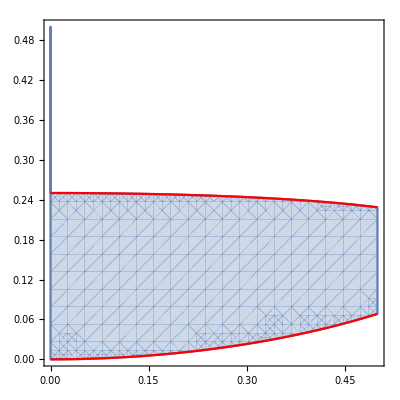

```mathematica
Show[RegionPlot[λnum[αin,sin]<1,{αin,0,0.5},{sin,0,0.5}],Plot[{critUpper[X,α]/.{X->1,Y->0},critLower[X,α]/.{X->1,Y->0}},{α,0,0.5},PlotStyle->Red]]
```

#### Figure S2

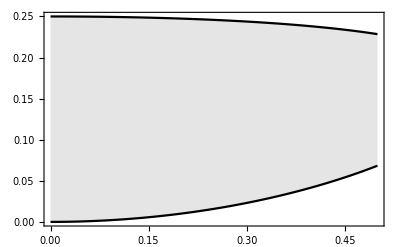

```mathematica
Plot[{critUpper[X,α]/.{X->1,Y->0},critLower[X,α]/.{X->1,Y->0}},{α,0,0.5},PlotStyle->Black,Filling->1->{2},FillingStyle->Directive[Gray],Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,14]]
Export[NotebookDirectory[]<>"Plots/SeedDormancy.pdf",%,ImageResolution->300];
```